# 3.1 Index of a fixed point

## Each of the following systems has a fixed point at . For each system, either draw a (rough) phase plot (for example using StreamPlot[]) and obtain the index, or evaluate the index using an analytical integral formula. You do not need to prepare and upload your phase plots in the parts a)-d) of this exercise, it is enough to upload the code you used to solve the problem (or StreamPlots if that was how you obtained the index). Moreover, you will not receive any feedback on the correctness of your answer for this exercise from OpenTA.

## a) Give the index for the fixed point of .

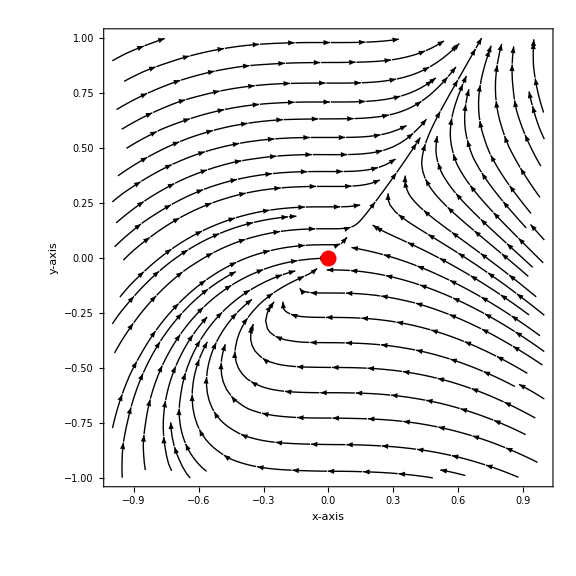

```mathematica
ClearAll["Global`*"]

equation1 = y-x;
equation2 = x^2;

StreamPlot[{equation1, equation2}, {x, -1, 1}, {y, -1, 1}, 
 PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black &), 
 StreamStyle -> Directive[Black], StreamColorFunction -> None,
 Epilog -> {Red, PointSize[0.02], Point[{0, 0}]},
 FrameLabel -> {{"y-axis", None}, {"x-axis", None}}]
```

## b) Give the index for the fixed point of the Cartesian system and corresponding to , , where and θ are polar coordinates. Let be a smooth function with for small values of and .

To solve this use the fact that in   the terms of  can be ignored. Thus we receive the following equation system.
		
		
Since we want to transform from polar to Cartesian coordinates we can use the x =  and . Since both  and it is possible to derivate with respect to . One then receives:
		
		
We know from above that , thus the equations become
		
		
Now for small  and ,  thus substitute to get
		
		
And in the last step substitute r according to x =  and   to get the transformed system:
		
		
While plotting one has to remember that there are two cases to check,  and . In both cases the index is equal to one. When changing the sign of  has the equivalent effect as changing time and thus the flow changes direction.

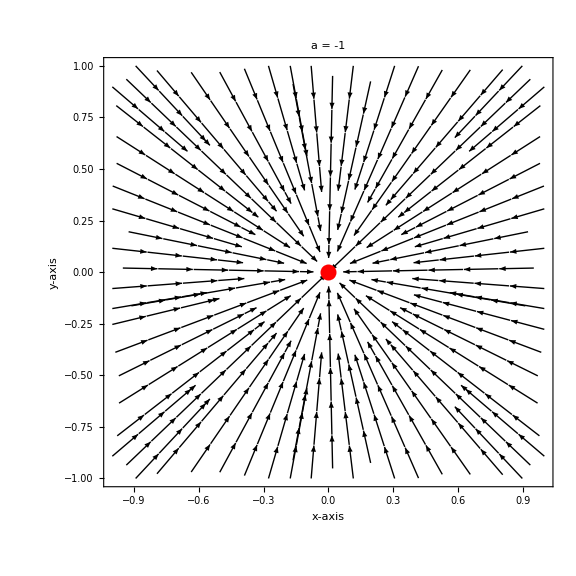

```mathematica
ClearAll["Global`*"]

equation1 = a*x;
equation2 = a*y;
a = -1;
StreamPlot[{equation1, equation2}, {x, -1, 1}, {y, -1, 1}, 
 PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black &), 
 StreamStyle -> Directive[Black], StreamColorFunction -> None,
 Epilog -> {Red, PointSize[0.02], Point[{0, 0}]},
 FrameLabel -> {{"y-axis", None}, {"x-axis", None}},
 PlotLabel -> "a = -1"]
```

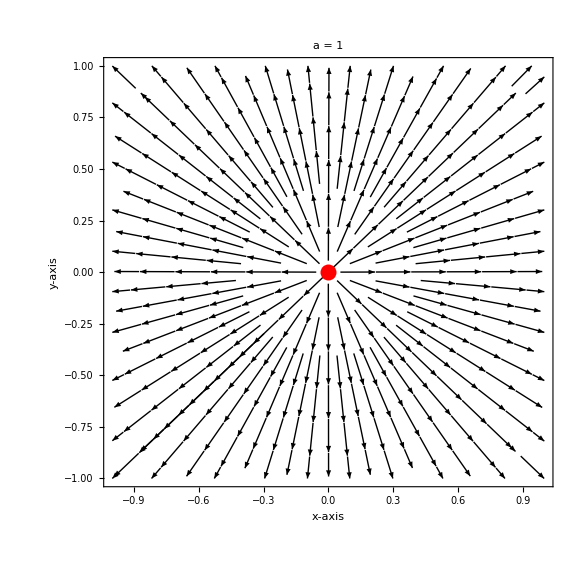

```mathematica
ClearAll["Global`*"]

equation1 = a*x;
equation2 = a*y;
a = 1;
StreamPlot[{equation1, equation2}, {x, -1, 1}, {y, -1, 1}, 
 PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black &), 
 StreamStyle -> Directive[Black], StreamColorFunction -> None,
 Epilog -> {Red, PointSize[0.02], Point[{0, 0}]},
 FrameLabel -> {{"y-axis", None}, {"x-axis", None}},
 PlotLabel -> "a = 1"]
```

## c) Give the index for the fixed point of .

As we can see from the plot this is a saddle point and the index is minus one.

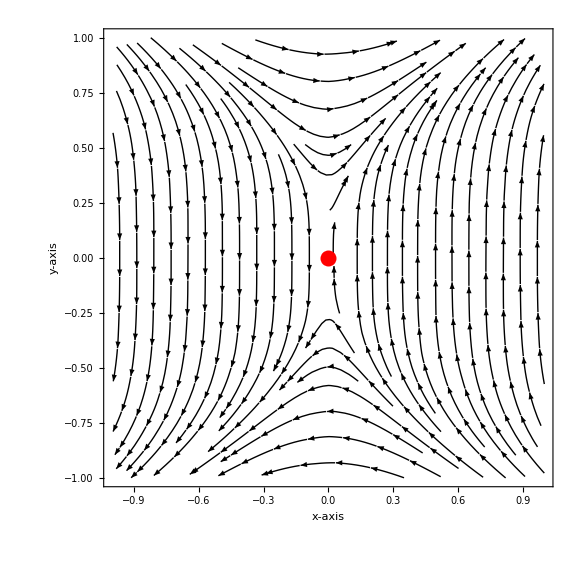

```mathematica
ClearAll["Global`*"]

equation1 = y^3;
equation2 = x;

StreamPlot[{equation1, equation2}, {x, -1, 1}, {y, -1, 1}, 
 PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black &), 
 StreamStyle -> Directive[Black], StreamColorFunction -> None,
 Epilog -> {Red, PointSize[0.02], Point[{0, 0}]},
 FrameLabel -> {{"y-axis", None}, {"x-axis", None}}]
```

## d) Give the index for the fixed point of , , where is a non-zero integer number and is evaluated on the suitable branch.

Given the two  dependent coordinates
		
		
originally three cases ought to be considered ,  and . The case , is not necessary for this task, but still somewhat interesting. 
While using interactive plots it is easy to check that the index is .

```mathematica
ClearAll["Global`*"]

equation1[n_, x_, y_] := (x^2 + y^2)^(Abs[n]/2) * Cos[n * ArcTan[y/x]];
equation2[n_, x_, y_] := (x^2 + y^2)^(Abs[n]/2) * Sin[n * ArcTan[y/x]];

Manipulate[
  StreamPlot[{equation1[n, x, y], equation2[n, x, y]}, {x, -1, 1}, {y, -1, 1},
    PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black &), 
    StreamStyle -> Directive[Black], StreamColorFunction -> None,
    Epilog -> {Red, PointSize[0.02], Point[{0, 0}]},
    FrameLabel -> {{"y-axis", None}, {"x-axis", None}},
    PlotLabel -> Row[{"n = ", n}]],
  {n, 1, 10, 1}
]
```

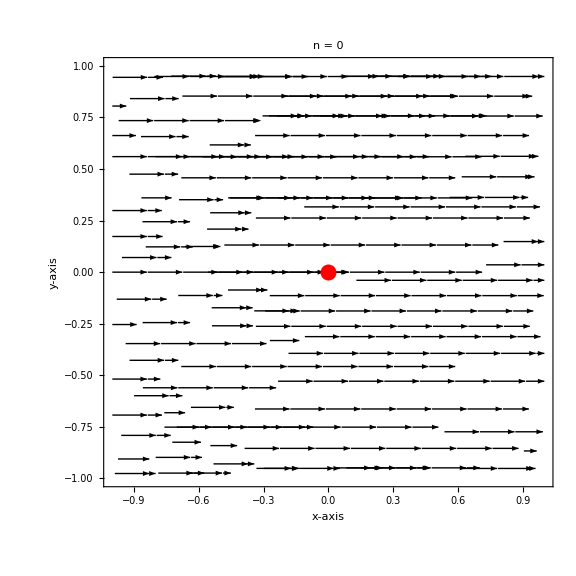

```mathematica
ClearAll["Global`*"]

equation1 = (x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]];
equation2 = (x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]];
n = 0;
StreamPlot[{equation1, equation2}, {x, -1, 1}, {y, -1, 1}, 
 PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black &), 
 StreamStyle -> Directive[Black], StreamColorFunction -> None,
 Epilog -> {Red, PointSize[0.02], Point[{0, 0}]},
 FrameLabel -> {{"y-axis", None}, {"x-axis", None}},
 PlotLabel -> "n = 0"]
```

```mathematica
ClearAll["Global`*"]

equation1[n_, x_, y_] := (x^2 + y^2)^(Abs[n]/2) * Cos[n * ArcTan[y/x]];
equation2[n_, x_, y_] := (x^2 + y^2)^(Abs[n]/2) * Sin[n * ArcTan[y/x]];

Manipulate[
  StreamPlot[{equation1[n, x, y], equation2[n, x, y]}, {x, -1, 1}, {y, -1, 1},
    PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black &), 
    StreamStyle -> Directive[Black], StreamColorFunction -> None,
    Epilog -> {Red, PointSize[0.02], Point[{0, 0}]},
    FrameLabel -> {{"y-axis", None}, {"x-axis", None}},
    PlotLabel -> Row[{"n = ", n}]],
  {n, -1, -10, 1}
]
```

If we have two equations 









Sometimes its much easier to transform to polar coordinates. 
, , ,